# Age distribution dynamics with stochastic jumps in mortality

## Analytical Results

#### Pdfs

```mathematica
p[y_,η_]:=HeavisideTheta[-y] ⅇ^(γ y) ((√(η γ λ) BesselI[1,2 √(η γ λ) √-y])/(√-y)+DiracDelta[-y])Exp[-λ η]
pp[y_,η_]:=p[y-yo+μd η,η]
pn[n_,η_]:=pp[Log[n],η]/n;
Pw[w_,λ_,γ_]:=(ι^(-γ-λ/μd)(μd)^(γ+1))/Beta[γ+1,λ/μd] w^γ(ι-μd w)^(λ/μd-1)
solnm=DSolve[{D[Nm[x],x]==-μd Nm[x]-λ Nm[x]+λ γ/(γ+1)Nm[x],Nm[0]==ι},Nm,x];
nm[x_]:=Nm[x]/.solnm
```

#### Pdfs μd=0

```mathematica
p2[y_,η_]:=HeavisideTheta[-y] ⅇ^(γ y) ((√(η γ λ) BesselI[1,2 √(η γ λ) √-y])/(√-y)+DiracDelta[-y])Exp[-λ η]
pp2[y_,η_]:=p2[y-yo,η]
pn2[n_,η_]:=pp2[Log[n],η]/n;
Pw2[w_,λ_,γ_]:=((λ/ι)^((1+1/γ)/(1/γ))Exp[-λ w/ι] w^γ)/Gamma[(1+1/γ)/(1/γ)];
solnm2=DSolve[{D[Nm[x],x]==-λ Nm[x]+λ γ/(γ+1)Nm[x],Nm[0]==ι},Nm,x];
nm2[x_]:=Nm[x]/.solnm2
```

## Figure 1

### Realization exported to Matlab for 3D graph

```mathematica
μd1=0.01;
λ1=0.1;
γ1=10;
timestepM=60; (*minutes, Change in time at each step*)
duration =200; (*days - Duration of simulation*)
Steps[Duration_,TimeStep_]:=(Duration*24*60)/TimeStep 
ν = {};
ν=RandomVariate[CompoundPoissonDistribution[λ1 timestepM/(60 24),ExponentialDistribution[γ1]],Steps[duration,timestepM]];
yy= {};
yy=Flatten[{yy,Log[ι]}];Do[yy=Flatten[{yy,-timestepM/(24*60)μd1 -ν[[t]]+yy[[t]]}], {t,Steps[duration,timestepM]}];NNe=Exp[yy];
```

```mathematica
NX=Table[t,{t,0,200,timestepM/(24*60)}];
```

```mathematica
Ntab=Transpose[{NNe,NX}];
```

```mathematica
Nt[t_,τ_]:=NNe[[τ]];
```

```mathematica
n=Table[{τ,5+τ,NNe[[τ]]},{τ,0,200*24}];
```

```mathematica
Export["n.dat",n]
```

n.dat

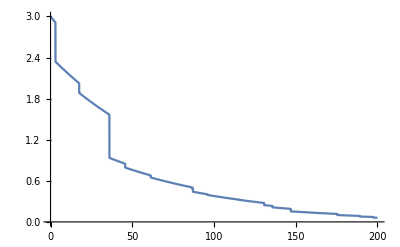

```mathematica
ListLinePlot[NNe,DataRange->{0,200},PlotRange->All]
```

## Figure 2

### Figure P_N

```mathematica
ι=3;
λ=0.1;
yo=Log[ι];
μd=0.05;
γ=10;
RightAxis=1.05;
LeftAxisMax=2.55;
LeftAxisMin=0;
TwoAxisPlot[{f_,g_},{x_,x0_,x1_},opts:OptionsPattern[]]:=Quiet[Module[{f0,f1,g0,g1,gp,scale,gticks},{f0,f1}=Options[Plot[f,{x,x0,x1},Frame->True,opts],PlotRange][[1,2,2]];
{g0,g1}=Options[gp=Plot[g,{x,x0,x1},Frame->True,opts],PlotRange][[1,2,2]];
scale[y_]:=LeftAxisMin+((LeftAxisMax-LeftAxisMin)*(y-g0))/(g1-g0);
gticks=Apply[{scale[#1],##2}&,AbsoluteOptions[gp,FrameTicks][[1,2,2]],{1}];
Plot[{f,scale[g]},{x,x0,x1},PlotRange->{{0,ι},{LeftAxisMin,LeftAxisMax}},Axes->False,Frame->{{True,True},{True,False}},LabelStyle->Directive[20, Bold,Black],FrameTicks->{{{(*{0,Rotate["0",90°]},*){.5,Rotate["0.5",90°]},{1,Rotate["1",90°]},{1.5,Rotate["1.5",90°]},{2,Rotate["2",90°]},{2.5,Rotate["2.5",90°]}},(*gticks*){(*{0,Rotate["0",90°]},*){.625,Rotate["0.25",90°]},{1.25,Rotate["0.5",90°]},{1.875,Rotate["0.75",90°]},{2.5,Rotate["1",90°]}}},{{0,.5,1,1.5,2,2.5,3},None}},FrameLabel->{{"p_N","p_atom"},{"n",None}},PlotStyle->{{GrayLevel[0],Opacity[0],Thick},{Opacity[0],Black,Thick}},(*GridLines-> Automatic,GridLinesStyle-> Directive[GrayLevel[.4],Thickness[.002],Dotted],*)FrameStyle->{{BaseStyle->Blue,BaseStyle->Yellow},{{},{}}},opts]]]

TwoAxis=TwoAxisPlot[{q,q RightAxis},{q,0,1},PlotStyle-> Red];
Fontsize=12;
Atom[s_]:=Integrate[(ⅇ^(-0.1 s+10 (0.05 s-Log[3]+Log[n])) (DiracDelta[-0.05 s+Log[3]-Log[n]]))/n,{n,0,Infinity}];
```

```mathematica
ι=3;
μd=0.05;
atmes5=Graphics[{EdgeForm[Directive[Thickness[.0045],GrayLevel[0.2]]],Opacity[0],Rectangle[{ι Exp[-μd 5]-0.02,0*ScaleFactor},{ι Exp[-μd 5]+0.02,1*Atom[5](LeftAxisMax-LeftAxisMin)* 1}]}];
ptau5=Plot[pn[n,5],{n,0,ι},PlotRange->All,PlotStyle->Directive[GrayLevel[0.2],Thickness[.01]],PlotLabels->Placed[{"η=5"},{2.5,1.4}],LabelStyle->Directive[Bold, 20,Background-> None]];
atmes10=Graphics[{EdgeForm[Directive[Thickness[.0045],GrayLevel[0.4]]],Opacity[0],Rectangle[{ι Exp[-μd 10]-0.02,0*ScaleFactor},{ι Exp[-μd 10]+0.02,1*Atom[10](LeftAxisMax-LeftAxisMin)* 1}]}];
ptau10=Plot[pn[n,10],{n,0,ι},PlotRange->All,PlotStyle->Directive[GrayLevel[0.4],Thickness[.01]],PlotLabels->Placed[{"η=10"},{2,2.1}],LabelStyle->Directive[Bold, 20,Background-> None]];
atmes15=Graphics[{EdgeForm[Directive[Thickness[.0045],GrayLevel[0.6]]],Opacity[0],Rectangle[{ι Exp[-μd 15]-0.02,0*ScaleFactor},{ι Exp[-μd 15]+0.02,1*Atom[15](LeftAxisMax-LeftAxisMin)* 1}]}];
ptau15=Plot[pn[n,15],{n,0,ι},PlotRange->All,PlotStyle->Directive[GrayLevel[0.6],Thickness[.01]],PlotLabels->Placed[{"η=15"},{1.25,2.5}],LabelStyle->Directive[Bold, 20,Background-> None]];
atmes20=Graphics[{EdgeForm[Directive[Thickness[.0045],GrayLevel[0.8]]],Opacity[0],Rectangle[{ι Exp[-μd 20]-0.02,0*ScaleFactor},{ι Exp[-μd 20]+0.02,1*Atom[20](LeftAxisMax-LeftAxisMin)* 1}]}];
ptau20=Plot[pn[n,20],{n,0,ι},PlotRange->All,PlotStyle->Directive[GrayLevel[0.8],Thickness[.01]],PlotLabels->Placed[{"η=20"},{1.6,2.4}],LabelStyle->Directive[Bold, 20,Background-> None]];
pN=Show[TwoAxis,ptau20,atmes20,ptau5,atmes5,ptau10,atmes10,ptau15,atmes15,ImageSize-> Large]
```

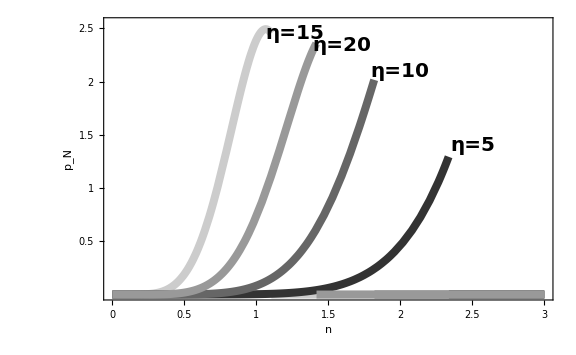

### Figure P_W

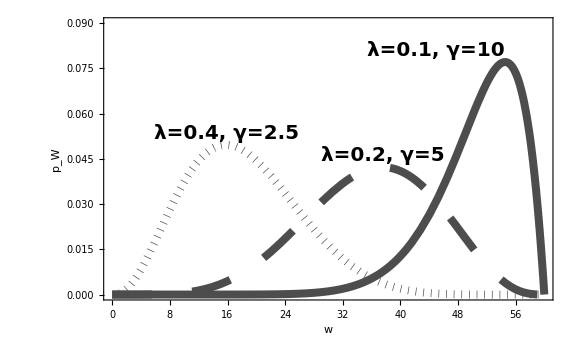

```mathematica
ι=3;
λ=0.1;
yo=Log[ι];
μd=0.05;
γ=10;
pw=Plot[{Pw[w,λ,γ],Pw[w,2λ,.5γ],Pw[w,4λ,.25γ]},{w,0,ι/μd},PlotRange->{{0,ι/μd},{0,0.09}},PlotStyle->{Directive[GrayLevel[0.3],Thickness[0.01]],Directive[GrayLevel[0.3],Thickness[0.01],Dashing[0.05]],Directive[GrayLevel[0.3],Thickness[0.01],Dotted]},LabelStyle->Directive[Bold, 20,Black],FrameLabel->{"w","p_W"},Frame->{{True,False},{True,False}},PlotLabels->{Placed[{"λ=0.1, γ=10"},Above],Placed[{"λ=0.2, γ=5"},Above],Placed[{"λ=0.4, γ=2.5"},Above]},Ticks->{Automatic, {0.02,0.04,.06,0.08}},ImageSize->Large]
```

## Figure 3

### Simulation

```mathematica
ι=3;
λ=0.1;
yo=Log[ι];
μd=0.05;
γ=10;
timestepM=60; (*minutes, Change in time at each step*)
duration =20; (*days - Duration of simulation*)
realizations=500;
Steps[Duration_,TimeStep_]:=(Duration*24*60)/TimeStep 
ν = {};
NN3=Table[0(*,{i,1,Steps[duration,timestepM]}*),{j,1,realizations}];
Do[ν=RandomVariate[CompoundPoissonDistribution[λ timestepM/(60 24),ExponentialDistribution[γ]],Steps[duration,timestepM]];yy= {};
yy=Flatten[{yy,Log[RandomVariate[ExponentialDistribution[1/ι]]]}];Do[yy=Flatten[{yy,-timestepM/(24*60)μd -ν[[t]]+yy[[t]]}], {t,Steps[duration,timestepM]}];NN3[[i]]=Exp[yy],{i,1,realizations}]
```

### Figure

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in i near {i} = {27.0466}. NIntegrate obtained 0.0000265505 and 6.12799×10^-7 for the integral and error estimates.

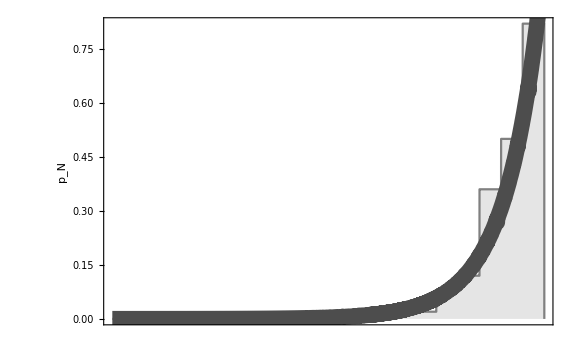

```mathematica
p2003=Rotate[Show[DiscretePlot[PDF[HistogramDistribution[-NN3[[All,24*20]]],x],{x,-10,0,0.001},PlotRange->Full,AxesLabel->{Framed["n",FrameStyle->None,FrameMargins->15],Framed["p_N",FrameStyle->None,FrameMargins->15]},Ticks->{{None}, {None}},Frame->{{True,False},{True,False}},FrameLabel->{{"p_N",None},{None,None}},FrameTicks->{{Automatic,None},{None,None}},LabelStyle->Directive[30,Black],PlotStyle->Gray],Plot[pnstar[n,20],{n,0,10},PlotStyle->Directive[Thickness[0.02],GrayLevel[0.3]],PlotRange->All,ScalingFunctions->{"Reverse",None}],ImageSize-> Large,Background->None],-90 Degree,{Center,Center}]
```

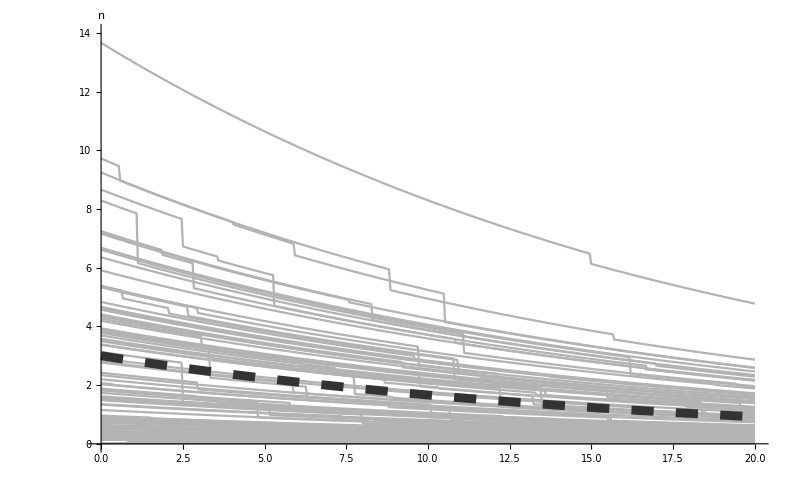
-Graphics-η

```mathematica
Figure42=Labeled[Show[ListLinePlot[Table[NN3[[i,1;;24*20]],{i,1,100}],PlotStyle->GrayLevel[0.7],PlotRange->{{0,20},{0,14}},AxesLabel->{None,"n"},LabelStyle->Directive[30,Black],DataRange->{0,20},Ticks->{Automatic, None},Background->None],Plot[nm4[x],{x,0,20},ImageSize->Large,PlotStyle->Directive[GrayLevel[0.2],Thickness[0.008],Dashing[0.02]],PlotRange->All,ImagePadding->{{20, 20}, {Automatic, 20}}],ImageSize->{800,500},PlotRange-> {{0,20},{0,14}}],η,Bottom,LabelStyle->Directive[30,Black,Bold]]
```

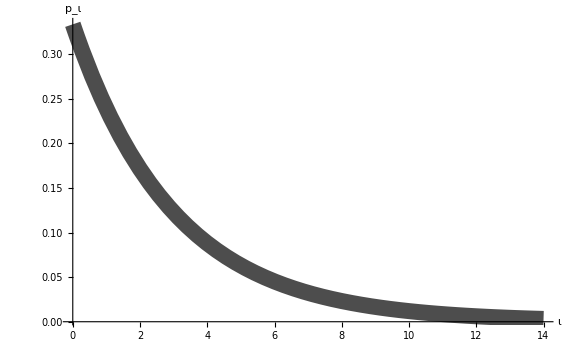

```mathematica
p41=Rotate[Show[Plot[1/3Exp[-1/3 x],{x,0,14},PlotStyle->Directive[Thickness[0.02],GrayLevel[0.3]],PlotRange->All,ImageSize-> Large,Background->None(*Frame->{{True,False},{True,False}},FrameLabel->{{"p_N",None},{"n",None}},FrameTicks->{{Automatic,None},{Automatic,None}}*),AxesLabel->{"ι",Framed["p_ι",FrameMargins->15,FrameStyle->None]},LabelStyle->Directive[30,Black],PlotStyle->Gray]],90 Degree,{Center,Center}]
```

## Figure 4

### Simulation

```mathematica
ι=0.054; (*g/m^2/d*)
λ=1.18 10^-2; (*1/d*)
yo=Log[ι];
μd=3 10^-4;
c=9.26 10^-2; (*1/cm/d*)
γ=0.93/c; (*1/cm*)
timestepM=24 60; (*minutes, Change in time at each step*)
duration =12 365; (*days - Duration of simulation*)
realizations=1000;
Steps[Duration_,TimeStep_]:=(Duration*24*60)/TimeStep 
ν = {};
w=Table[0,{j,1,realizations}];
Do[ν=RandomVariate[CompoundPoissonDistribution[λ timestepM/(60 24),ExponentialDistribution[γ]],Steps[duration,timestepM]];ww= {};
ww=Flatten[{ww,0}];Do[ww=Flatten[{ww,timestepM/(24*60)(ι-μd ww[[t]]) +(Exp[Log[ww[[t]]]-ν[[t]]]-ww[[t]])+ww[[t]]}], {t,Steps[duration,timestepM]}];w[[i]]=ww,{i,1,realizations}];
pwap=HistogramDistribution[-w[[All,Steps[duration,timestepM]]]];
```

### Figure

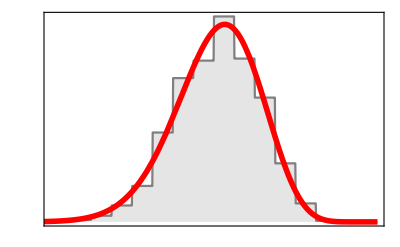

```mathematica
Show[DiscretePlot[PDF[pwap,x],{x,-80,0,0.1},PlotRange->All,PlotStyle->Gray,LabelStyle->Directive[Black, 20],Frame->{{False,True},{True,False}},FrameLabel->{{None,Framed["p_W_salt",BaseStyle->{25},FrameStyle->None]},{None,None}},FrameTicks->{{None,{{1 10^-2,"1x10^-2"},{2 10^-2,"2x10^-2"},{3 10^-2,"3x10^-2"}}},{None,None}}],Plot[Pw[w,λ,γ],{w,0,ι/μd},PlotRange->All,ScalingFunctions->{"Reverse",None},Ticks-> {None,Automatic},PlotStyle->Directive[Red,Thickness[0.01]]]]
```

```mathematica
α=(γ+λ/μd+1)/(γ+1);
wm[t_,wo_]:=(ⅇ^(-t α μd) (-ι+ⅇ^(t α μd) ι+wo α μd))/(α μd);
```

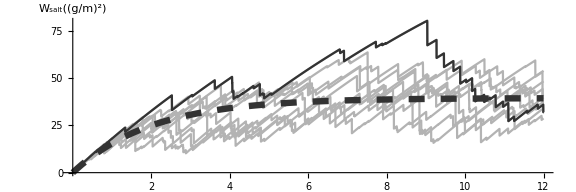

```mathematica
Show[ListLinePlot[w[[1;;10]],DataRange->{0,12 365},PlotRange->{Automatic,{0,80}},PlotStyle->Directive[GrayLevel[0.7]],TicksStyle->{Directive[FontOpacity->0,FontSize->0],Automatic},LabelStyle->Directive[20,Black],AxesLabel-> {None,Framed[Row[{"W_salt",,("(g/m")^2,")"}],FrameMargins->10,FrameStyle->None]},Ticks-> {{{2 365,"2"},{4 365,"4"},{6 365,"6"},{8 365,"8"},{10 365,"10"},{12 365,"12"}},Automatic}],ListLinePlot[w[[1]],DataRange->{0,12 365},PlotStyle->Directive[GrayLevel[0.2]]],Plot[wm[t,0],{t,0,12 365},PlotStyle->Directive[GrayLevel[0.2],Thickness[0.008],Dashing[0.02]]],ImageSize->Large,AspectRatio-> 1/3
]
```

```mathematica
a=Table[0,{j,1,realizations}];
Do[aa={};aa=Flatten[{aa,0}];Do[aa=Flatten[{aa,timestepM/(24*60)(Exp[-aa[[t-1]]]-ι/w[[i,t]] )+aa[[t-1]]}], {t,2,Steps[duration,timestepM]}];a[[i]]=Exp[aa],{i,1,realizations}];
```

```mathematica
A=Mean[a[[All]]];
```

```mathematica
pa=HistogramDistribution[-a[[All,Steps[duration,timestepM]]]];
```

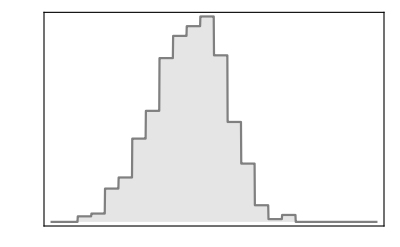

```mathematica
Show[DiscretePlot[PDF[pa,x],{x,-1200,0,1},PlotStyle->Gray,LabelStyle->Directive[Black, 20],Frame->{{False,True},{True,False}},FrameLabel->{{None,Framed["p_((T̄)_salt)",BaseStyle->{25},FrameStyle->None]},{None,None}},FrameTicks->{{None,{{1 10^-3,"1x10^-3"},{2 10^-3,"2x10^-3"},{3 10^-3,"3x10^-3"}}},{None,None}}]]
```

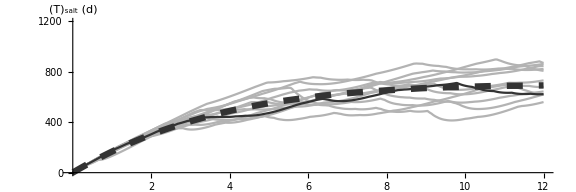
-Graphics-t(yr)

```mathematica
Labeled[Show[ListLinePlot[a[[10;;20]],DataRange->{0,12 365},PlotRange->{Automatic,{0,1200}},PlotStyle->Directive[GrayLevel[0.7]],LabelStyle->Directive[20,Black],AxesLabel-> {None,Framed["(T̄)_salt (d)",FrameStyle->None,FrameMargins->10]},Ticks-> {{{2 365,"2"},{4 365,"4"},{6 365,"6"},{8 365,"8"},{10 365,"10"},{12 365,"12"}},Automatic},ImageSize->Large,AspectRatio->1/3],ListLinePlot[a[[1]],DataRange->{0,12 365},PlotStyle->Directive[GrayLevel[0.2]]],ListLinePlot[A,DataRange->{0,12 365},PlotStyle->Directive[GrayLevel[0.2],Thickness[0.008],Dashing[0.02]]]],Row[{Style["t",Italic],"(yr)"}],LabelStyle->Directive[Black, 20]]
```

```mathematica
ι=0.054; (*g/m^2/d*)
λ=1.18 10^-2; (*1/d*)
yo=Log[ι];
μd=3 10^-4;
c=9.26 10^-2; (*1/cm/d*)
γ=0.93/c; (*1/cm*)
```

```mathematica
Subscript[T, h]=γ/(γ μd+λ)
```

678.001

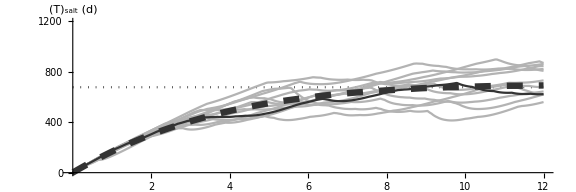
-Graphics-t(yr)

```mathematica
Labeled[Show[Plot[678,{t,0,12 365},PlotStyle->{Dotted,Thick,GrayLevel[0.1]}],-Graphics-,LabelStyle->Directive[20,Black],PlotRange->{Automatic,{0,1200}},AxesLabel-> {None,Framed["(T̄)_salt (d)",FrameStyle->None,FrameMargins->10]},Ticks-> {{{2 365,"2"},{4 365,"4"},{6 365,"6"},{8 365,"8"},{10 365,"10"},{12 365,"12"}},Automatic},ImageSize->Large,AspectRatio->1/3],Row[{Style["t",Italic],"(yr)"}],LabelStyle->Directive[Black, 20]]
```

## Figure 5

### Simulation 1

```mathematica
ι=0.054; (*g/m^2/d*)
λ=1.18 10^-2; (*1/d*)
yo=Log[ι];
μd=3 10^-4;       (*1/d*)
c=9.26 10^-2; (*1/cm/d*)
γ=0.93/c; (*1/cm*)
timestepM=24 60; (*minutes, Change in time at each step*)
duration =10 365; (*days - Duration of simulation*)
realizations=1000;
Steps[Duration_,TimeStep_]:=(Duration*24*60)/TimeStep 
ν = {};
NN=Table[0(*,{i,1,Steps[duration,timestepM]}*),{j,1,realizations}];
Do[ν=RandomVariate[CompoundPoissonDistribution[λ timestepM/(60 24),ExponentialDistribution[γ]],Steps[duration,timestepM]];yy= {};
yy=Flatten[{yy,Log[ι]}];Do[yy=Flatten[{yy,-timestepM/(24*60)μd -ν[[t]]+yy[[t]]}], {t,Steps[duration,timestepM]}];NN[[i]]=Exp[yy],{i,1,realizations}]
wsim=Table[Total[NN[[i,All]]]/24,{i,1,realizations}];
pws=HistogramDistribution[wsim] (*Numerical PDF for W*)
(*pmean=Table[Mean[NN[[All,i]]],{i,1,duration}];*)
```

DataDistribution[…]

```mathematica
Clear[NN]
```

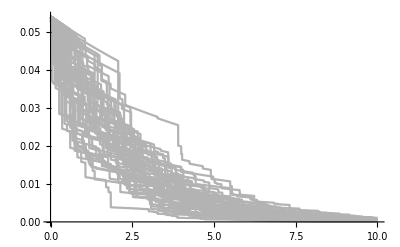

```mathematica
ListLinePlot[Table[NN[[i,1;;10 365]],{i,1,50}],PlotStyle->GrayLevel[0.7],PlotRange->All,DataRange->{0,10}]
```

```mathematica
(*NN=Import["/Users/Sasi/Desktop/NN.dat"];
```

```mathematica
Export["NN.dat",NN]
```

```mathematica
pmean=Table[Mean[NN[[All,i]]],{i,1,24 100}];
```

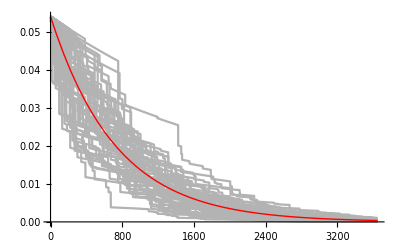

```mathematica
Show[ListLinePlot[Table[NN[[i,1;;10 365]],{i,1,50}],PlotStyle->GrayLevel[0.7],PlotRange->All,DataRange->{0,10 365}],Plot[nm[x],{x,0,10 365},PlotStyle->Directive[Thick,Red],PlotRange->All](*ListLinePlot[pmean,PlotStyle->Thick,DataRange->{0,100}]*)]
```

```mathematica
pnn=HistogramDistribution[NN[[All,20*10]]]
```

DataDistribution[…]

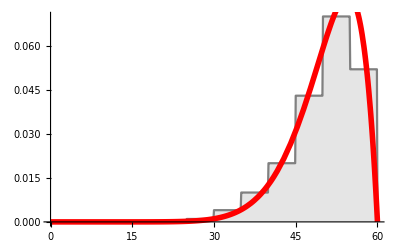

```mathematica
Show[DiscretePlot[PDF[pws,x],{x,0,ι/μd,0.1},PlotRange->All,PlotStyle->Gray],Plot[Pw[w],{w,0,ι/μd},PlotRange->All,PlotStyle->Directive[Red,Thickness[0.01]]]]
```

### Figure Application 1

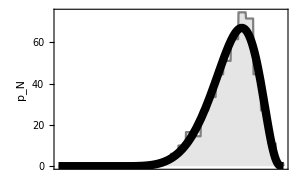

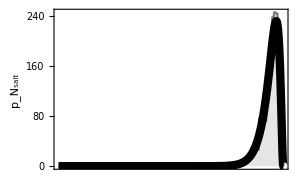

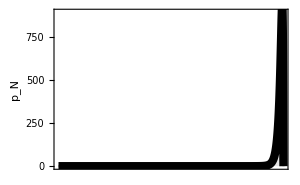

```mathematica
p1000=Rotate[Show[DiscretePlot[PDF[HistogramDistribution[-NN[[All,1000]]],x],{x,-0.06,0,0.0001},PlotRange->Full,FrameLabel->{{"p_N",None},{None,None}},Frame->{{True,False},{True,False}},FrameTicks->{{Automatic,None},{None,None}},LabelStyle->Directive[10,Black],PlotStyle->Gray],Plot[pn[n,1000],{n,0,0.06},PlotStyle->Directive[Thickness[0.02],Black],LabelStyle->Directive[20,Black],FrameLabel->{{Framed["p_N_salt",BaseStyle->35,FrameStyle->None],None},{None,None}},Frame->{{True,False},{True,False}},FrameTicks->{{{0,30,60},None},{None,None}},ScalingFunctions->{"Reverse",None},PlotRange->All],ImageSize-> {300,200},Background->None],-90 Degree,{Center,Center}]
p2000=Rotate[Show[DiscretePlot[PDF[HistogramDistribution[-NN[[All,2000]]],x],{x,-0.06,0,0.0001},PlotRange->Full,FrameLabel->{{Framed["p_N_salt",BaseStyle->40,FrameStyle->None],None},{None,None}},Frame->{{True,False},{True,False}},FrameTicks->{{Automatic,None},{None,None}},LabelStyle->Directive[10,Black],PlotStyle->Gray],Plot[pn[n,2000],{n,0,0.06},PlotStyle->Directive[Thickness[0.02],Black],LabelStyle->Directive[25,Black],FrameLabel->{{Framed["p_N_salt",BaseStyle->40,FrameStyle->None],None},{None,None}},Frame->{{True,False},{True,False}},FrameTicks->{{{0,100,200},None},{None,None}},ScalingFunctions->{"Reverse",None},PlotRange->All],ImageSize-> {300,200},Background->None],-90 Degree,{Center,Center}]
p3000=Rotate[Show[DiscretePlot[PDF[HistogramDistribution[-NN[[All,3000]]],x],{x,-0.06,0,0.0001},PlotRange->Full,FrameLabel->{{"p_N",None},{None,None}},Frame->{{True,False},{True,False}},FrameTicks->{{Automatic,None},{None,None}},LabelStyle->Directive[10,Black],PlotStyle->Gray],Plot[pn[n,3000],{n,0,0.06},PlotStyle->Directive[Thickness[0.02],Black],LabelStyle->Directive[30,Black],FrameLabel->{{Framed["p_N_salt",BaseStyle->45,FrameStyle->None],None},{None,None}},Frame->{{True,False},{True,False}},FrameTicks->{{{0,400,800},None},{None,None}},ScalingFunctions->{"Reverse",None},PlotRange->All],ImageSize-> {300,200},Background->None],-90 Degree,{Center,Center}]
```

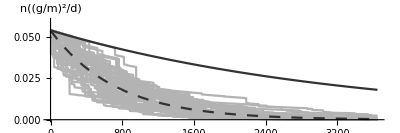
-Graphics-τ(d)

```mathematica
Figure21=Labeled[Show[ListLinePlot[Table[NN[[i,1;;10 365]],{i,1,50}],PlotStyle->GrayLevel[0.7],ImageSize->Full,PlotRange->All,AxesLabel->{None,Row[{Style["n",Italic],,("(g/m")^2,"/d)"}]},LabelStyle->Directive[40,Black],DataRange->{0,10 365},Background->None],Plot[ι Exp[-μd x],{x,0,10 365},PlotStyle->Directive[GrayLevel[0.2],Thickness[0.004]]],Plot[nm[x],{x,0,10 365},PlotStyle->Directive[GrayLevel[0.2],Thickness[0.004],Dashing[0.02]],PlotRange->All,ImagePadding->{{20, 20}, {Automatic, 20}}](*,Epilog->{Inset[p30,{30,2.2}],Inset[p60,{60,Center}],Inset[p90,{90,Center}]}*),AspectRatio-> 1/3,PlotRange-> {{0,10 365},{0,0.06}}],Row[{Style["τ",Italic,Bold],"(d)"}],Bottom,LabelStyle->Directive[50,Black]]
(*Figure22=Labeled[Show[DiscretePlot[PDF[pws,x],{x,0,ι/μd,0.01},PlotRange->{{0,ι/μd},{0,0.1}},AxesLabel->{None,Framed["p_W",FrameStyle->None,FrameMargins->15]},Ticks->{{10,30,50},{.02,.05,.08}},LabelStyle->Directive[30,Black],PlotStyle->Gray],Plot[Pw[w,λ,γ],{w,0,ι/μd},PlotRange->{{0,ι/μd},{0,0.1}},PlotStyle->Directive[Red,Thickness[0.01]]],ImageSize-> Large],w,Bottom,LabelStyle->Directive[30,Black]];
```

## Figure 6

### Simulation 2

```mathematica
ι=0.054; (*g/m^2/d*)
λ=1.18 10^-2; (*1/d*)
yo=Log[ι];
μd=3 10^-4;
c=9.26 10^-2; (*1/cm/d*)
γ=0.93/c; (*1/cm*)
timestepM=24 60; (*minutes, Change in time at each step*)
duration =10 365; (*days - Duration of simulation*)
realizations=1000;
Steps[Duration_,TimeStep_]:=(Duration*24*60)/TimeStep 
ν = {};
NN2=Table[0(*,{i,1,Steps[duration,timestepM]}*),{j,1,realizations}];
Do[ν=RandomVariate[CompoundPoissonDistribution[λ timestepM/(60 24),ExponentialDistribution[γ]],Steps[duration,timestepM]];yy= {};
yy=Flatten[{yy,Log[ι]}];Do[yy=Flatten[{yy,-ν[[t]]+yy[[t]]}], {t,Steps[duration,timestepM]}];NN2[[i]]=Exp[yy],{i,1,realizations}]
wsim2=Table[Total[NN2[[i,All]]],{i,1,realizations}];
pws2=HistogramDistribution[wsim2] (*Numerical PDF for W*)
pmean2=Table[Mean[NN2[[All,i]]],{i,1,Steps[duration,timestepM]}];
```

DataDistribution[…]

### Figure

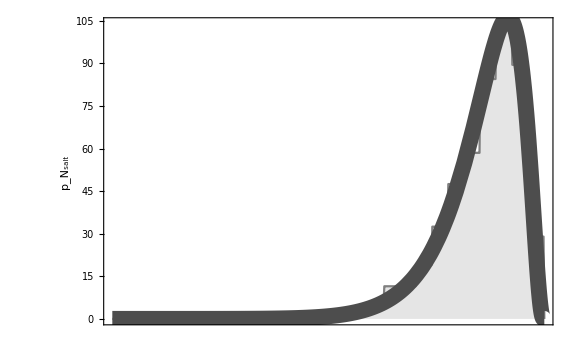

```mathematica
p2002=Rotate[Show[DiscretePlot[PDF[HistogramDistribution[-NN2[[All,5 365]]],x],{x,-ι,0,0.0001},PlotRange->Full,Ticks->{{None}, {None}},Frame->{{True,False},{True,False}},FrameLabel->{{"p_N_salt",None},{None,None}},FrameTicks->{{Automatic,None},{None,None}},LabelStyle->Directive[40,Black],PlotStyle->Gray],Plot[pn2[n,5 365],{n,0,ι},PlotStyle->Directive[Thickness[0.02],GrayLevel[0.3]],PlotRange->All,ScalingFunctions->{"Reverse",None}],ImageSize-> Large,Background->None],-90 Degree,{Center,Center}]
```

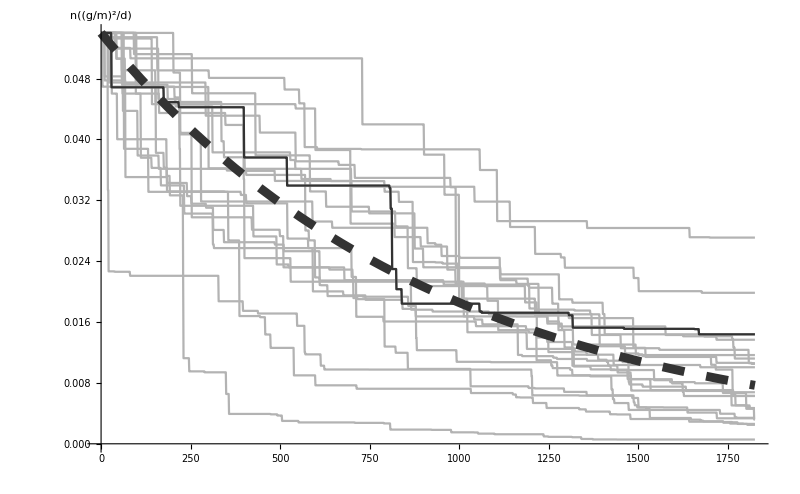
-Graphics-τ(d)

```mathematica
Figure31=Labeled[Show[ListLinePlot[Table[NN2[[i,1;;5 365]],{i,1,20}],PlotStyle->GrayLevel[0.7],PlotRange->All,AxesLabel->{None,Row[{Style["n",Italic],,("(g/m")^2,"/d)"}]},LabelStyle->Directive[40,Black],DataRange->{0,5 365},Background->None],ListLinePlot[NN2[[1,1;;5 365]],PlotStyle->GrayLevel[0.2],PlotRange->All,AxesLabel->{None,"n"},LabelStyle->Directive[30,Black],DataRange->{0,5 365},Background->None],Plot[nm2[x],{x,0,5 365},ImageSize->Large,PlotStyle->Directive[GrayLevel[0.2],Thickness[0.008],Dashing[0.02]],PlotRange->All,ImagePadding->{{20, 20}, {Automatic, 20}}],ImageSize->{800,500},PlotRange-> {{0,5 365},{0,ι}}],Row[{Style["τ",Italic,Bold],"(d)"}],Bottom,LabelStyle->Directive[30,Black]]
```

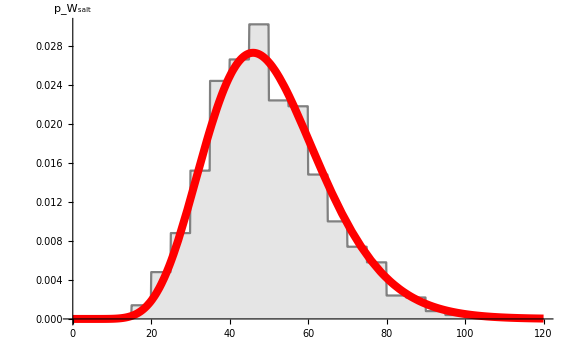
-Graphics-w(g/m^2)

```mathematica
Figure33=Labeled[Show[DiscretePlot[PDF[pws2,x],{x,0,120,0.1},PlotRange->All,AxesLabel->{None,Framed["p_W_salt",FrameStyle->None,FrameMargins->15]},LabelStyle->Directive[30,Black],PlotStyle->Gray],Plot[Pw2[w,λ,γ],{w,0,120},PlotStyle->Directive[Red,Thickness[0.01]]],ImageSize-> Large],Row[{Style["w",Italic],"(g/m^2)"}],Bottom,LabelStyle->Directive[40,Black]]
```

```mathematica
Export["Figure31.pdf",Figure31];
Export["Figure32.pdf",p2002];
Export["Figure33.pdf",Figure33];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Figure31.pdf"]]]
```